# インパクトファクターの算出

## Thomsonによるインパクトファクターの算出:

A = 1992年における被引用数
B = 1990 - 91年に出版された論文が1992年に引用された数 (Aの部分集合)
C = 1990 - 91年に出版された論文数
D = B/C = 1992年のインパクトファクター

## Link: top | prev

## アニメーションによる解説:

以上webコンテンツ

## インパクトファクター算出のアニメーション

ここでは、インパクトファクター算出を説明するスライドを作ってみます。

データ取得の期間を6年とし、仮想的な雑誌”A”をの被引用を設定します。雑誌”A”には年間2-3本の論文が含まれるとします。

```mathematica
yearscitation=2
```

2

```mathematica
dataspan=6
```

6

```mathematica
pubofjournal["A"]={{2,1},{2,2},{3,3},{2,4},{3,5},{3,6}}
```

{{2,1},{2,2},{3,3},{2,4},{3,5},{3,6}}

論文をノードで表すため、下記によりその座標を決定します。

```mathematica
vecofjournal["A"]=Map[Table[{#[[2]],2/(#[[1]]+1)*n},{n,#[[1]]}]&,pubofjournal["A"]]
```

{{{1,2/3},{1,4/3}},{{2,2/3},{2,4/3}},{{3,1/2},{3,1},{3,3/2}},{{4,2/3},{4,4/3}},{{5,1/2},{5,1},{5,3/2}},{{6,1/2},{6,1},{6,3/2}}}

```mathematica
pointofjournal["A"]=Flatten[Map[Point[#]&,vecofjournal["A"],{-2}]]
```

{Point[{1,2/3}],Point[{1,4/3}],Point[{2,2/3}],Point[{2,4/3}],Point[{3,1/2}],Point[{3,1}],Point[{3,3/2}],Point[{4,2/3}],Point[{4,4/3}],Point[{5,1/2}],Point[{5,1}],Point[{5,3/2}],Point[{6,1/2}],Point[{6,1}],Point[{6,3/2}]}

被引用誌のノードには色をつけてみます。

```mathematica
numofcolors=Tr[Map[#[[1]]&,pubofjournal["A"]]]
```

15

```mathematica
colors=Table[ColorData["Rainbow",1/(numofcolors+1)*n],{n,numofcolors}];
```

```mathematica
colorpointofjournal["A"]=Inner[List,colors,pointofjournal["A"],List];
```

```mathematica
colormaprules=Table[Flatten[vecofjournal["A"],1][[m]]->colors[[m]],{m,numofcolors}];
```

雑誌”A”を引用する論文のノードを設定します。

```mathematica
citingjournals={{5,1},{4,2},{5,3},{4,4},{5,5},{6,6}}
```

{{5,1},{4,2},{5,3},{4,4},{5,5},{6,6}}

下記により各論文の座標を設定します。

```mathematica
vecofcitingjournals=Map[Table[{#[[2]],(2/(#[[1]]+1)*n)-2},{n,#[[1]]}]&,citingjournals]
```

{{{1,-5/3},{1,-4/3},{1,-1},{1,-2/3},{1,-1/3}},{{2,-8/5},{2,-6/5},{2,-4/5},{2,-2/5}},{{3,-5/3},{3,-4/3},{3,-1},{3,-2/3},{3,-1/3}},{{4,-8/5},{4,-6/5},{4,-4/5},{4,-2/5}},{{5,-5/3},{5,-4/3},{5,-1},{5,-2/3},{5,-1/3}},{{6,-12/7},{6,-10/7},{6,-8/7},{6,-6/7},{6,-4/7},{6,-2/7}}}

```mathematica
pointofcitigjournals=Flatten[Map[Point[#]&,vecofcitingjournals,{-2}]];
```

これから、引用関係を表すパスを設定しますが、その前に被引用のノードの色をパスにマップするルールを設定しておきます。

```mathematica
colormaprules=Table[Flatten[vecofjournal["A"],1][[m]]->colors[[m]],{m,numofcolors}];
```

引用関係を設定します。

```mathematica
pairs={
{{1,1},{3,1}},
{{1,2},{5,2}},
{{1,2},{6,1}},
{{2,1},{4,2}},
{{2,1},{6,2}},
{{2,2},{4,2}},
{{2,2},{5,2}},
{{2,2},{5,1}},
{{3,1},{5,1}},
{{3,2},{5,1}},
{{3,2},{6,2}},
{{4,1},{5,1}},
{{4,1},{6,1}},
{{4,2},{6,2}},
{{5,1},{6,1}},
{{5,2},{6,2}}
}
```

{{{1,1},{3,1}},{{1,2},{5,2}},{{1,2},{6,1}},{{2,1},{4,2}},{{2,1},{6,2}},{{2,2},{4,2}},{{2,2},{5,2}},{{2,2},{5,1}},{{3,1},{5,1}},{{3,2},{5,1}},{{3,2},{6,2}},{{4,1},{5,1}},{{4,1},{6,1}},{{4,2},{6,2}},{{5,1},{6,1}},{{5,2},{6,2}}}

すべての引用関係のパスを設定します。

```mathematica
alllines={Gray,Dashed,Map[Line[{vecofjournal["A"][[#[[1, 1]], #[[1, 2]]]], vecofcitingjournals[[#[[2, 1]], #[[2, 2]]]]} ]&, pairs]}
```

{GrayLevel[0.5],Dashing[{Small,Small}],{Line[{{1,2/3},{3,-5/3}}],Line[{{1,4/3},{5,-4/3}}],Line[{{1,4/3},{6,-12/7}}],Line[{{2,2/3},{4,-6/5}}],Line[{{2,2/3},{6,-10/7}}],Line[{{2,4/3},{4,-6/5}}],Line[{{2,4/3},{5,-4/3}}],Line[{{2,4/3},{5,-5/3}}],Line[{{3,1/2},{5,-5/3}}],Line[{{3,1},{5,-5/3}}],Line[{{3,1},{6,-10/7}}],Line[{{4,2/3},{5,-5/3}}],Line[{{4,2/3},{6,-12/7}}],Line[{{4,4/3},{6,-10/7}}],Line[{{5,1/2},{6,-12/7}}],Line[{{5,1},{6,-10/7}}]}}

3年インパクトファクターとして有効な引用をピックアップします。

```mathematica
effectivecite=Cases[pairs,x_/;x[[1,1]]<x[[2,1]]&&x[[1,1]]>=x[[2,1]]-yearscitation]
```

{{{1,1},{3,1}},{{2,1},{4,2}},{{2,2},{4,2}},{{3,1},{5,1}},{{3,2},{5,1}},{{4,1},{5,1}},{{4,1},{6,1}},{{4,2},{6,2}},{{5,1},{6,1}},{{5,2},{6,2}}}

評価に係わるパスを設定します。

```mathematica
effectivelines={Map[Line[{vecofjournal["A"][[#[[1, 1]], #[[1, 2]]]], vecofcitingjournals[[#[[2, 1]], #[[2, 2]]]]} ]&, effectivecite]}
```

{{Line[{{1,2/3},{3,-5/3}}],Line[{{2,2/3},{4,-6/5}}],Line[{{2,4/3},{4,-6/5}}],Line[{{3,1/2},{5,-5/3}}],Line[{{3,1},{5,-5/3}}],Line[{{4,2/3},{5,-5/3}}],Line[{{4,2/3},{6,-12/7}}],Line[{{4,4/3},{6,-10/7}}],Line[{{5,1/2},{6,-12/7}}],Line[{{5,1},{6,-10/7}}]}}

```mathematica
Table[path[n-yearscitation,n]=Cases[effectivecite,x_/;x[[2,1]]==n],{n,yearscitation+1,dataspan}]
```

{{{{1,1},{3,1}}},{{{2,1},{4,2}},{{2,2},{4,2}}},{{{3,1},{5,1}},{{3,2},{5,1}},{{4,1},{5,1}}},{{{4,1},{6,1}},{{4,2},{6,2}},{{5,1},{6,1}},{{5,2},{6,2}}}}

各論文の被引用に色をマップします。

```mathematica
For[i=1+yearscitation,i<=dataspan,i++,
Print[i];
vec[i-yearscitation,i]=Map[{vecofjournal["A"][[#[[1,1]],#[[1,2]]]],vecofcitingjournals[[#[[2,1]],#[[2,2]]]]}&,path[i-yearscitation,i]];
line[i-yearscitation,i,"color"]=Map[{#[[1]]/.colormaprules,Line[#]}&,vec[i-yearscitation,i]];
]
```

3

4

5

6

その他の部品を作ります。

```mathematica
journalText["A"]={FontSize->16,Text["被引用誌\"A\"",{7,1}]}
```

{FontSize→16,Text[被引用誌"A",{7,1}]}

```mathematica
citingjournalText={FontSize->16,Text["引用誌
(Aを含む複数)",{7,-1}]}
```

{FontSize→16,Text[引用誌
(Aを含む複数),{7,-1}]}

```mathematica
boundary={Gray,Thick,Line[{{0,0},{8,0}}]}
```

{GrayLevel[0.5],Thickness[Large],Line[{{0,0},{8,0}}]}

```mathematica
timespan[0]={White,Thickness[0.01],Line[{{1,-3},{7,-3}}]}
```

{GrayLevel[1],Thickness[0.01],Line[{{1,-3},{7,-3}}]}

```mathematica
Table[
timespan[n,n+yearscitation]={Thickness[0.01],Line[{{n-0.1,-2},{n+yearscitation+0.1,-2}}]},
{n,dataspan}]
```

{{Thickness[0.01],Line[{{0.9,-2},{3.1,-2}}]},{Thickness[0.01],Line[{{1.9,-2},{4.1,-2}}]},{Thickness[0.01],Line[{{2.9,-2},{5.1,-2}}]},{Thickness[0.01],Line[{{3.9,-2},{6.1,-2}}]},{Thickness[0.01],Line[{{4.9,-2},{7.1,-2}}]},{Thickness[0.01],Line[{{5.9,-2},{8.1,-2}}]}}

各年度の表示

```mathematica
year=Table[Text[IntegerString[n+1989],{n,2}],{n,6}]
```

{Text[1990,{1,2}],Text[1991,{2,2}],Text[1992,{3,2}],Text[1993,{4,2}],Text[1994,{5,2}],Text[1995,{6,2}]}

```mathematica
yeartext=Prepend[year,FontSize->14]
```

{FontSize→14,Text[1990,{1,2}],Text[1991,{2,2}],Text[1992,{3,2}],Text[1993,{4,2}],Text[1994,{5,2}],Text[1995,{6,2}]}

説明文を作ります。

```mathematica
regend[0]={FontSize->20,Text["6年間の引用データがあります。ドットは論文を表し、
線は引用を表します。",{4,-3},{0,-1}]};
```

```mathematica
regend[1]={FontSize->20,Text["算出には3年間分のデータが必要です。この図では4年分の
インパクトファクターを算出できます。",{4,-3},{0,-1}]};
```

```mathematica
regend[2]={FontSize->20,Text["3年のうち、最初の2年分の出版(C)が次の1年間でどれだけ
引用されたか(B) : B/Cがインパクトファクターです。",{4,-3},{0,-1}]};
```

```mathematica
regend[3]={FontSize->20,Text["1994年のインパクトファクターは、被引用数(3)/論文数(5) = 0.6 です。",{4,-3},{0,-1}]};
```

```mathematica
regend[4]={FontSize->20,Text["1995年のインパクトファクターは、被引用数(4)/論文数(5) = 0.8 です。",{4,-3},{0,-1}]};
```

```mathematica
regend[5]={FontSize->20,Text["評価された引用を実線で塗りつぶすと、全ての
引用が評価されるわけではないと解かります。",{4,-3},{0,-1}]};
```

アニメーションを作る。

```mathematica
isize={720,440}
```

{720,440}

```mathematica
g[0]=Graphics[{
boundary,
alllines,
journalText["A"],
citingjournalText,
yeartext,
PointSize[0.03],
pointofcitigjournals,
colorpointofjournal["A"],
timespan[0],
regend[0]
},ImageSize->isize];
```

```mathematica
For[i=1,i<=dataspan-yearscitation,i++,
g[i]=Graphics[{
boundary,
alllines,
journalText["A"],
citingjournalText,
yeartext,
PointSize[0.03],
pointofcitigjournals,
colorpointofjournal["A"],
timespan[i,i+2],
regend[i],
line[i,i+2,"color"]
},ImageSize->isize]
]
```

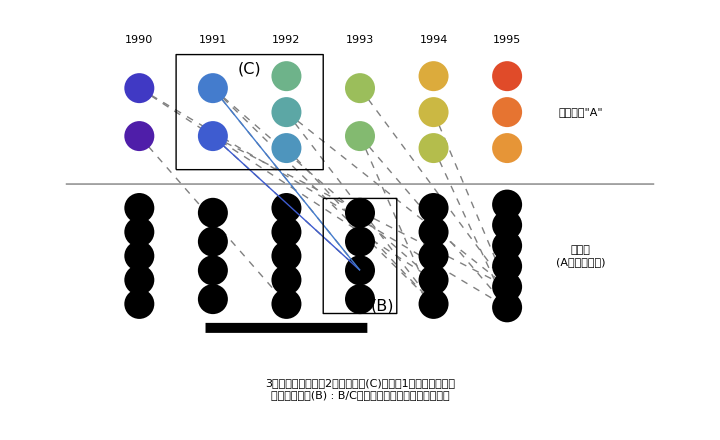

```mathematica
g[2]=Graphics[{
boundary,
alllines,
journalText["A"],
citingjournalText,
yeartext,
PointSize[0.03],
pointofcitigjournals,
colorpointofjournal["A"],
timespan[2,2+2],
regend[2],
line[2,2+2,"color"],
RGBColor[0,0,0],Line[{{1.5,0.2},{1.5,1.8},{3.5,1.8},{3.5,0.2},{1.5,0.2}}],Text[Style["(C)",16],{2.5,1.6}],
Line[{{3.5,-0.2},{3.5,-1.8},{4.5,-1.8},{4.5,-0.2},{3.5,-0.2}}],
Text[Style["(B)",16],{4.3,-1.7}]
},ImageSize->isize]
```

```mathematica
g[5]=Graphics[{
boundary,
alllines,
journalText["A"],
citingjournalText,
yeartext,
PointSize[0.03],
pointofcitigjournals,
colorpointofjournal["A"],
regend[5],
effectivelines
},ImageSize->isize];
```

```mathematica
ListAnimate[{g[0],g[1],g[2],g[3],g[4],g[5]}]
```

## メモ

Thomsonによる説明(http://thomsonreuters.com/products_services/science/free/essays/impact_factor/ アクセス:2012-02-22).

Calculation for journal impact factor.
A = total cites in 1992
B = 1992 cites to articles published in 1990 - 91 (this is a subset of A)
C = number of articles published in 1990 - 91
D = B/C = 1992 impact factor

雑誌インパクトファクターの算出:
A = 1992年における被引用数
B = 1990 - 91年に出版された論文が1992年に引用された数 (Aの部分集合)
C = 1990 - 91年に出版された論文数
D = B/C = 1992年のインパクトファクター

Calculation for five-year impact factor: One year of citations to five years of articles.
A= citations in 1992 to articles published in 1987-91
B= articles published in 1987-91
C= A/B = five-year impact factor

Calculation for impact factor revised to exclude self-citations.
A= citations in 1992 to articles published in 1990-91
B= 1992 self-citations to articles published in 1990-91
C= A - B = total citations minus self-citations to recent articles
D= number of articles published 1990-91
E= revised impact factor (C/D)

Unified 1992 impact factor calculation for title change. 
A=1992 citations to articles published in 1990-91 (a1 + a2)
    A1=those for new title
    A2=those for superseded title 

B=number of articles published in 1990-91 (B1 + B2)
    B1=those for new title
    B2=those for superseded title 

C=unified impact factor (A/B)
    C1=A1/B1 = JCR® factor for the new title 
    C2=A2/B2 = JCR factor for the superseded title

## 作業記録

コンテンツは天野が用意する。

アニメ作成は、大川さんにコマを渡して動画を作成してもらう。